# ЛР3 (Бусько Егор, 3 вариант)

## task 1

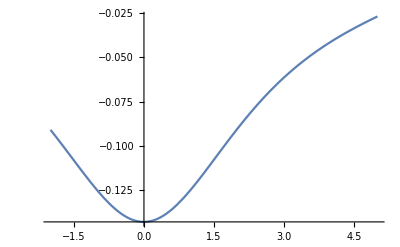

```mathematica
f[x_]:=(E^(x-7)-1)/(x^2+7);
eps = 10^-6;
Plot[f[x],{x,-2,5}]
```

```mathematica
Simp[f_,{a_,b_}]:=Module[
{M,hsimp,Nsimp,Isimp},
M=First[FindMaximum[{Abs[D[f[x],{x,4}]],a≤ x≤b},{x,a}]];
hsimp=((180eps)/M)^(1/4);
Nsimp = Round[(b-a)/hsimp];
Isimp=hsimp/3*(f[a]+f[b]+4Sum[f[a +k*hsimp],{k,1,Nsimp-1,2}]
+2Sum[f[a+k*hsimp],{k,2,Nsimp-2,2}]);
Return[{Isimp,Nsimp}];
];
```

```mathematica
Print["Метод Симпсона: ",Simp[f,{-1,9}]]
```

Метод Симпсона: {-0.521031,28}

```mathematica
Gauss[f_,{a_,b_}]:=Module[
{P,R,Ig,A,k,x,roots,n},
P[x_,n_]:=1/(2^n n!)*D[(x^2-1)^n,{x,n}];
R[f,n_]:=2^(2n+3)/((2n+3)!)(((n+1)!)/((2n+2)!))^2*First[FindMaximum[{Abs[D[f[(b-a)/2 x+(a+b)/2],{x,2n+2}]],-1≤ x≤1},{x,-1}]];
k=0;
While[R[f,k]>eps,
n=k+1;
roots=x/.Solve[P[x,n]== 0];
A[k_]:=2/((1-(roots⟦k+1⟧)^2)*(D[P[x,n],x]/.x->roots⟦k+1⟧)^2);
Ig = (b-a)/2 Sum[A[i]*f[(b-a)/2 roots⟦i+1⟧+(a+b)/2],{i,0,k}];
k++
];
Return[{Ig//N,k}];
];
```

```mathematica
Print["Метод Гаусса: ",Gauss[f,{-1,9}]]
NIntegrate[f[x],{x,-1,9}]
```

Метод Гаусса: {-0.512392,5}

-0.512428

## task 2

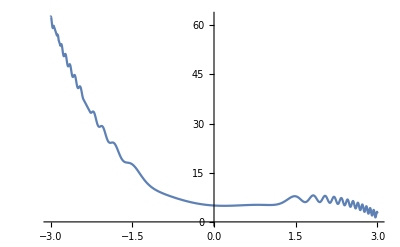

```mathematica
g[x_]:=-x^3+3 x^2-x+5-Sin[x^4];
eps=10^-6;
Plot[g[x],{x,-3,3}]
```

Точка максимума по методу половинного деления: (1.48117 , 7.84588) получена на 20 шаге

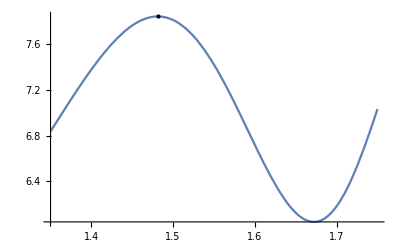

```mathematica
MaxDihotom[f_,a_,b_]:={
a1=a;
b1=b;
k=1;
Do[
x0=(a1+b1)/2//N;
f1=f[x0+eps]//N;
f2=f[x0-eps]//N;
If[f1<f2,b1=x0,a1=x0];
k++;
If[Abs[b1-a1]<eps,Break[]],{i,1,100}]
Print["Точка максимума по методу половинного деления: ","(",x0//N," , ",f[x0]//N,")", " получена на ",k," шаге"];
gr1=Plot[f[x],{x,a,b}];
gr2=Graphics[Point[{x0, f[x0]}]];
Show[gr1,gr2]
}
MaxDihotom[g,27/20,7/4]
```

Точка минимума по методу половинного деления: (1.67223 , 6.04128) получена на 20 шаге

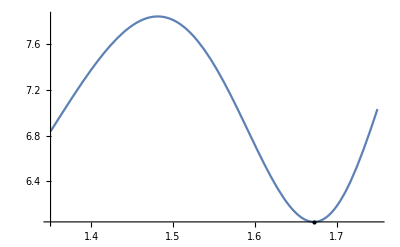

```mathematica
MinDihotom[f_,a_,b_]:={
a1=a;
b1=b;
k=1;
Do[
x0=(a1+b1)/2//N;
f1=f[x0+eps]//N;
f2=f[x0-eps]//N;
If[f1<f2,a1=x0,b1=x0];
k++;
If[Abs[b1-a1]<eps,Break[]],{i,1,100}]
Print["Точка минимума по методу половинного деления: ","(",x0//N," , ",f[x0]//N,")", " получена на ",k," шаге"];
gr1=Plot[f[x],{x,a,b}];
gr2=Graphics[Point[{x0, f[x0]}]];
Show[gr1,gr2]
}
MinDihotom[g,27/20,7/4]
```

Точка максимума по методу золотого сечения: (1.48126 , 7.84588) получена на 15 шаге

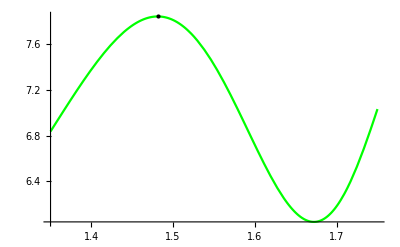

```mathematica
goldSectionMax[f_,a_,b_]:={
a1=a;
b1=b;
k=1;
t=(1+√5)/2//N;
Do[
x1=b1-(b1-a1)/t//N;
x2=a1+(b1-a1)/t//N;
y1=f[x1];
y2=f[x2];
If[y1≥y2,b1=x1,a1=x2];
k++;
If[Abs[b1-a1]<eps,Break[]],{i,1,100}]
Print["Точка максимума по методу золотого сечения: ","(",(a1+b1)/2//N," , ",f[(a1+b1)/2]//N,")", " получена на ",k," шаге"];
gr1=Plot[f[x],{x,a,b},PlotStyle->Green];
gr2=Graphics[Point[{(a1+b1)/2, f[(a1+b1)/2]}]];
Show[gr1,gr2]
}
goldSectionMax[g,27/20,7/4]
```

Точка минимума по методу золотого сечения: (1.67223 , 6.04128) получена на 28 шаге

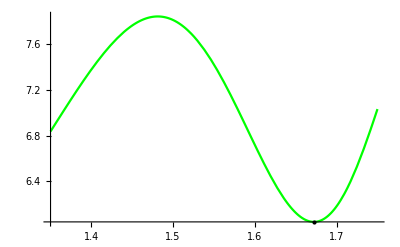

```mathematica
goldSectionMin[f_,a_,b_]:={
a1=a;
b1=b;
k=1;
t=(1+√5)/2//N;
Do[
x1=b1-(b1-a1)/t//N;
x2=a1+(b1-a1)/t//N;
y1=f[x1];
y2=f[x2];
If[y1≥y2,a1=x1,b1=x2];
k++;
If[Abs[b1-a1]<eps,Break[]],{i,1,100}]
Print["Точка минимума по методу золотого сечения: ","(",(a1+b1)/2//N," , ",f[(a1+b1)/2]//N,")", " получена на ",k," шаге"];
gr1=Plot[f[x],{x,a,b},PlotStyle->Green];
gr2=Graphics[Point[{(a1+b1)/2, f[(a1+b1)/2]}]];
Show[gr1,gr2]
}
goldSectionMin[g,27/20,7/4]
```

```mathematica
Maximize[{g[x],27/20≤x≤7/4},{x},Reals]//N
Minimize[{g[x],27/20≤x≤7/4},{x},Reals]//N
```

{7.84588,{x→1.48117}}

{6.04128,{x→1.67223}}